```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}];
```

/Users/zack/Documents/ignition/cantera/ratematrix

## Random matrices

data/test2

{902,7,0.0068792}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

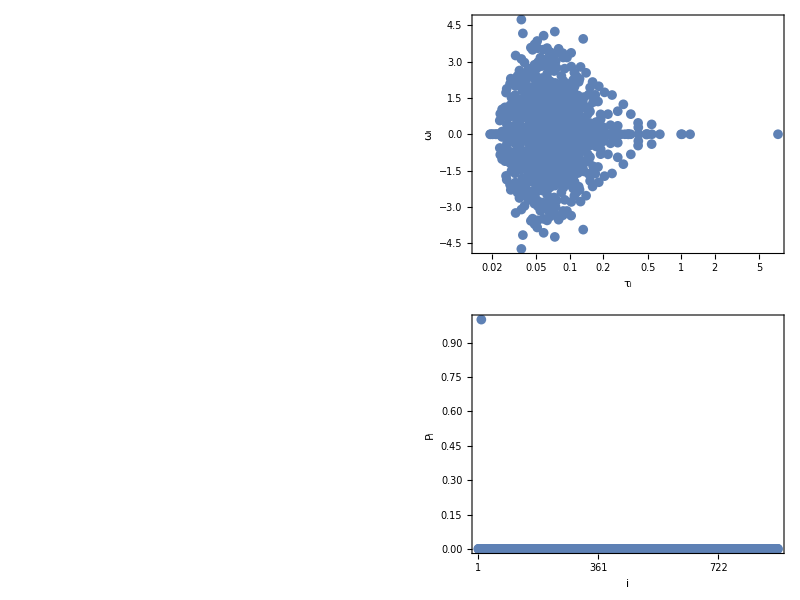

```mathematica
filebase="data/random2"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
A=SparseArray[Table[{columns[[i]]+1,rows[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}},MaxPlotPoints->200]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
```

```mathematica
data
```

$Failed⟦17;;-1⟧

```mathematica
filebase="data/random2"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
MatrixPlot[A-DiagonalMatrix[Diagonal[A]],ImageSize->1000,AspectRatio->1,ColorFunctionScaling->False,ColorFunction->cf2,FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},FrameLabel->{{i,None},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{80,25}},DataReversed->{False,False},MaxPlotPoints->2^12]
```

data/random2

Import::nffil: File data/random2out.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Set::shape: Lists {dim,ns,runtime} and $Failed⟦1⟧ are not the same shape.

$Failed⟦1⟧

BinaryReadList::noopen: Cannot open data/random2rows.npy.

Part::take: Cannot take positions 17 through -1 in $Failed.

BinaryReadList::noopen: Cannot open data/random2columns.npy.

Part::take: Cannot take positions 17 through -1 in $Failed.

BinaryReadList::noopen: Cannot open data/random2data.npy.

Part::take: Cannot take positions 17 through -1 in $Failed.

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Diagonal::list: List expected at position 1 in Diagonal[SparseArray[{{1+$Failed,1+$Failed}→$Failed,{1+17;;-1,1+17;;-1}→17;;-1},{dim,dim}]].

MatrixPlot::mat0: Argument -DiagonalMatrix[Diagonal[SparseArray[{{Plus[«2»],Plus[«2»]}→$Failed,{Plus[«2»],Plus[«2»]}→17;;-1},{dim,dim}]]]+SparseArray[{{1+$Failed,1+$Failed}→$Failed,{1+17;;-1,1+17;;-1}→17;;-1},{dim,dim}] at position 1 is not a matrix.

MatrixPlot[-DiagonalMatrix[Diagonal[SparseArray[{{1+$Failed,1+$Failed}→$Failed,{1+17;;-1,1+17;;-1}→17;;-1},{dim,dim}]]]+SparseArray[{{1+$Failed,1+$Failed}→$Failed,{1+17;;-1,1+17;;-1}→17;;-1},{dim,dim}],ImageSize→1000,AspectRatio→1,ColorFunctionScaling→False,ColorFunction→cf2,FrameTicks→{{{1,Round[1+1/5 (-1+dim)],Round[1+2/5 (-1+dim)],Round[1+3/5 (-1+dim)],Round[1+4/5 (-1+dim)],Round[dim]},{{1,},{Round[1+1/5 (-1+dim)],},{Round[1+2/5 (-1+dim)],},{Round[1+3/5 (-1+dim)],},{Round[1+4/5 (-1+dim)],},{Round[dim],}}},{{1,Round[1+1/5 (-1+dim)],Round[1+2/5 (-1+dim)],Round[1+3/5 (-1+dim)],Round[1+4/5 (-1+dim)],Round[dim]},{{1,},{Round[1+1/5 (-1+dim)],},{Round[1+2/5 (-1+dim)],},{Round[1+3/5 (-1+dim)],},{Round[1+4/5 (-1+dim)],},{Round[dim],}}}},FrameLabel→{{i,None},{j,None}},LabelStyle→Directive[16,GrayLevel[0]],FrameStyle→Directive[GrayLevel[0],AbsoluteThickness[2]],ImagePadding→{{80,25},{80,25}},DataReversed→{False,False},MaxPlotPoints→4096]

```mathematica
Eigenvalues[A+Transpose[A]]
```

Eigenvalues::arh: Because finding 10602 out of the 10602 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

$Aborted

data/test2

{877,7,0.00677526}

10.4118

{19.4623,Null}

0.000047553

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

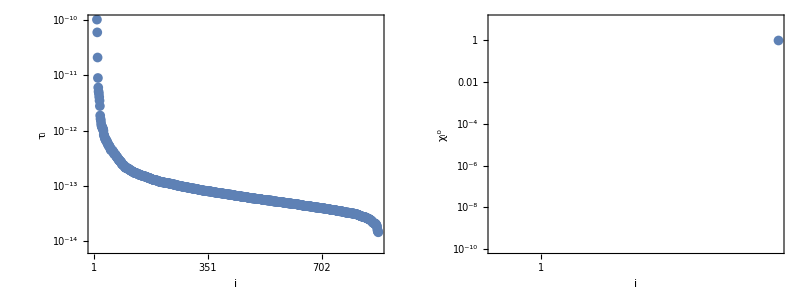

fig3.pdf

0.778408

```mathematica
filebase="data/test2"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=1;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
r=1/2;
AbsoluteTiming[angles=ParallelTable[ArcCos[Abs[evecs[[-i]].Conjugate[evecs[[-j]]]]/(Norm[evecs[[-i]]]*Norm[evecs[[-j]]])],{i,1,Length[evecs]},{j,1,Length[evecs]}];]
max=Pi/8;
r=1/2;
cf=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*(Pi/2-#)/max]&;
max2=N[Max[A/10^18]]
cf2=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*#/max2]&;;
p=Grid[{{Show[rasterizeBackground[MatrixPlot[Abs[A]/10^18,ImageSize->350,AspectRatio->r,ColorFunctionScaling->False,ColorFunction->cf2,FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[{Round[i],""},{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},FrameLabel->{{None,None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{True,False},MaxPlotPoints->200]],Epilog->Inset[BarLegend[{cf2,{0,max2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->DisplayForm[RowBox[{Subsuperscript[W,i,k],"/",HoldForm[10^18]}]]],ImageScaled[{0.55,0.8}]]],Show[rasterizeBackground[MatrixPlot[angles,ImageSize->350,AspectRatio->r,PlotRange->All,FrameTicks->{Table[Round[i],{i,1,Length[evecs],(Length[evecs]-1)/5}],Table[{Round[i],""},{i,1,Length[evecs],(Length[evecs]-1)/5}]},FrameLabel->{{None,
None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{True,False},ColorFunctionScaling->False,ColorFunction->cf]],Epilog->Inset[BarLegend[{cf,{Pi/2-max,Pi/2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->Subsuperscript[θ,i,k]],ImageScaled[{0.55,0.8}]]]},{ListLogPlot[Reverse[-1/Re[evals[[1;;-2]]]],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript[τ,i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImagePadding->{{80,25},{65,10}},ImageSize->350,FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],ListLogPlot[Abs[evecs[[-1]]],PlotRange->{10^-10,10},Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subsuperscript[χ,i,0]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]]}}]
Export["fig3.pdf",p]
Total[Abs[evals]^2]/Total[svals^2]
```

## h2o2 matrices

data/test

{376,9,0.15109}

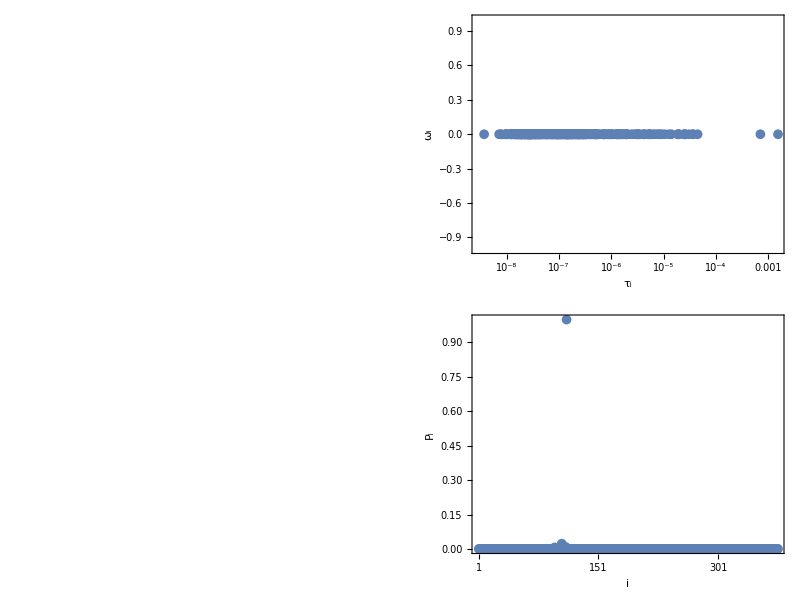

{60 (Ar_1)+O_1 H_1+6 (O_1 H_2),60 (Ar_1)+H_1+H_2+5 (O_1 H_2)+O_2,60 (Ar_1)+H_1+O_1+6 (O_1 H_2),60 (Ar_1)+2 (H_2)+O_1 H_1+4 (O_1 H_2)+O_2,60 (Ar_1)+H_2+O_1+O_1 H_1+5 (O_1 H_2)}

2417.89

2.31557

-3.72794×10^-9+0. ⅈ

```mathematica
filebase="data/test"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
Total[spforms*#]&/@multiindices[[Reverse[Ordering[Abs[evecs[[-1]]]]][[1;;5]]]]
Re[Total[temperatures*evecs[[-1]]]/Total[evecs[[-1]]]]
Re[Total[pressures*evecs[[-1]]]/Total[evecs[[-1]]]]
1/evals[[1]]
```

data/test

{376,9,0.15109}

1.92531×10^-13

18.729

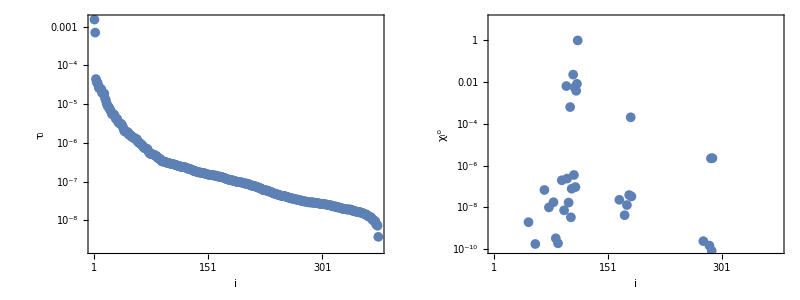

fig1.pdf

0.657416

```mathematica
filebase="data/test"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=1;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
r=1/2;
angles=ParallelTable[ArcCos[Abs[evecs[[-i]].Conjugate[evecs[[-j]]]]/(Norm[evecs[[-i]]]*Norm[evecs[[-j]]])],{i,1,Length[evecs]},{j,1,Length[evecs]}];
max=Pi/8;
r=1/2;
cf=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*(Pi/2-#)/max]&;
max2=N[Max[A/10^18]]
cf2=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*#/max2]&;;
p=Grid[{{Show[rasterizeBackground[MatrixPlot[Abs[A]/10^18,ImageSize->350,AspectRatio->r,ColorFunctionScaling->False,ColorFunction->cf2,FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[{Round[i],""},{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},FrameLabel->{{None,None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{True,False}]],Epilog->Inset[BarLegend[{cf2,{0,max2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->DisplayForm[RowBox[{Subsuperscript[W,i,k],"/",HoldForm[10^18]}]]],ImageScaled[{0.55,0.8}]]],Show[rasterizeBackground[MatrixPlot[angles,ImageSize->350,AspectRatio->r,PlotRange->All,FrameTicks->{Table[Round[i],{i,1,Length[evecs],(Length[evecs]-1)/5}],Table[{Round[i],""},{i,1,Length[evecs],(Length[evecs]-1)/5}]},FrameLabel->{{None,
None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{True,False},ColorFunctionScaling->False,ColorFunction->cf]],Epilog->Inset[BarLegend[{cf,{Pi/2-max,Pi/2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->Subsuperscript[θ,i,k]],ImageScaled[{0.55,0.8}]]]},{ListLogPlot[Reverse[-1/Re[evals[[1;;-2]]]],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript[τ,i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImagePadding->{{80,25},{65,10}},ImageSize->350,FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],ListLogPlot[Abs[evecs[[-1]]],PlotRange->{10^-10,10},Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subsuperscript[χ,i,0]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]]}}]
Export["fig1.pdf",p]
Total[Abs[evals]^2]/Total[svals^2]
```

## Concentration evolutions

data/h2o2/

{417.349,Null}

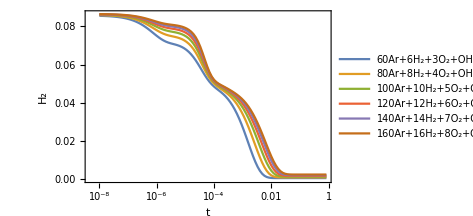
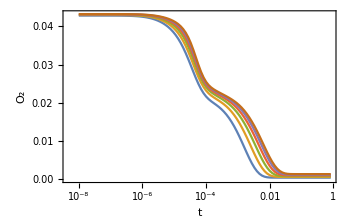
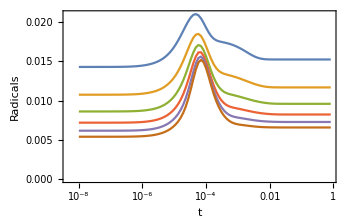
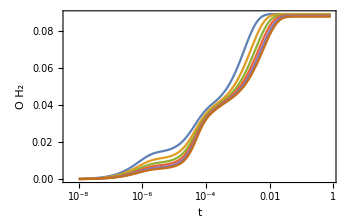
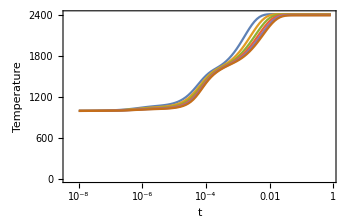
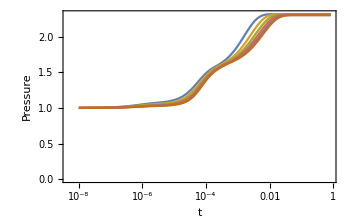

```mathematica
o2dats={};
h2dats={};
h2odats={};
radicaldats={};
temperaturedats={};
pressuredats={};
initials={};
filebase0="data/h2o2/"
AbsoluteTiming[Monitor[Do[filebase=filebase0<>ToString[m]<>"/";
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
ind=1;
initial=Total[DeleteCases[If[#[[1]]>0, If[#[[1]]==1,DisplayForm[RowBox[{ToString[#[[2]]]}]], DisplayForm[RowBox[{#[[1]],#[[2]]}]]]]&/@Transpose[Table[{multiindices[[i]],spforms},{i,1,dim}][[ind]]],Null]];
AppendTo[initials,initial];
states=Partition[BinaryReadList[filebase<>"propogate.npy","Real64"][[17;;-1]],dim];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
o2norm=DiagonalMatrix[((#[[4]])/Total[#])&/@multiindices];
h2norm=DiagonalMatrix[((#[[1]])/Total[#])&/@multiindices];
h2onorm=DiagonalMatrix[((#[[6]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices];
temperaturenorm=DiagonalMatrix[temperatures];
pressurenorm=DiagonalMatrix[pressures];
(*Abs[(Total[#]-Total[evecs[[-1]].h2norm]/Total[evecs[[-1]]])]*)
AppendTo[h2dats,Transpose[{times,Total[#]&/@(states.h2norm)}]];
AppendTo[o2dats,Transpose[{times,Total[#]&/@(states.o2norm)}]];
AppendTo[radicaldats,Transpose[{times,Total[#]&/@(states.radicalnorm)}]];
AppendTo[h2odats,Transpose[{times,Total[#]&/@(states.h2onorm)}]];
AppendTo[temperaturedats,Transpose[{times,Total[#]&/@(states.temperaturenorm)}]];
AppendTo[pressuredats,Transpose[{times,Total[#]&/@(states.pressurenorm)}]];
p=Legended[ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]];,{m,3,8}],{m,n, p}]]
p=Legended[{{ListLogLinearPlot[h2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[o2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[h2odats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[temperaturedats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[pressuredats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}},Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]]
```

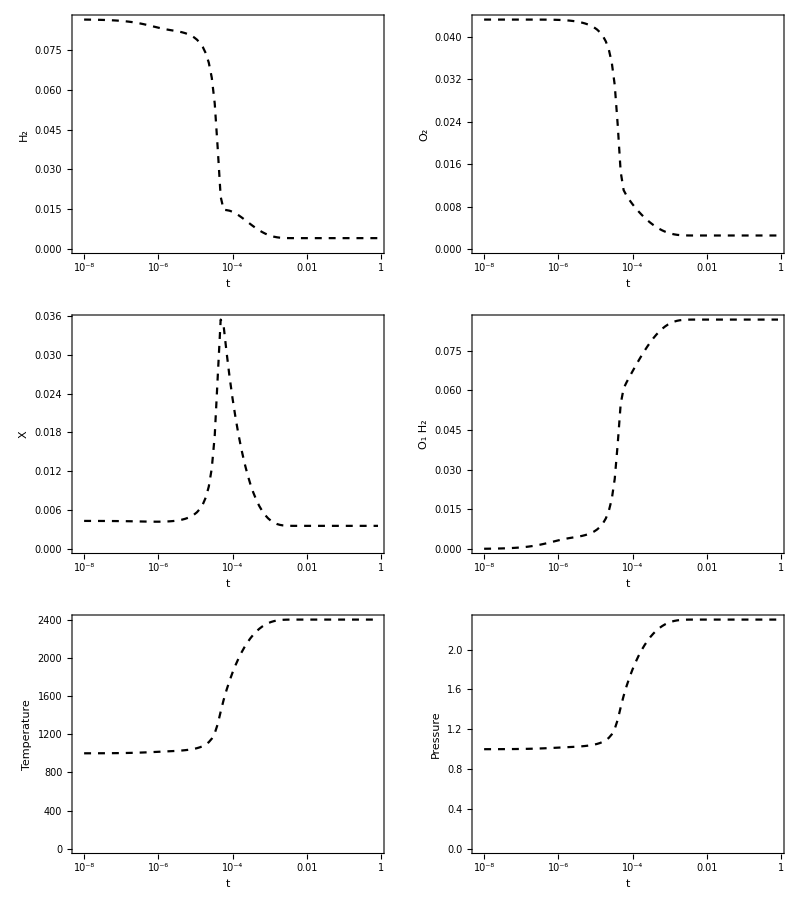

```mathematica
dat=Import["data/h2o2.csv"];
{{p0,p1},{p2,p3},{p4,p5}}={{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,4]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,7]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,5]]+dat[[2;;-1,6]]+dat[[2;;-1,8]]+dat[[2;;-1,10]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,X},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,9]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,2]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,3]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]}};
Grid[{{p0,p1},{p2,p3},{p4,p5}}]
```

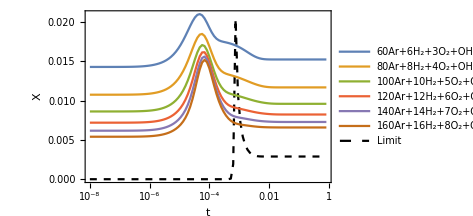

```mathematica
p=Legended[Show[p2,ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,X},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],PlotRange->All],Placed[LineLegend[Join[ColorData[97,"ColorList"][[1;;Length[initials]]],{Directive[Black,Dashed]}],Join[initials,{"Limit"}]],Right]]
```

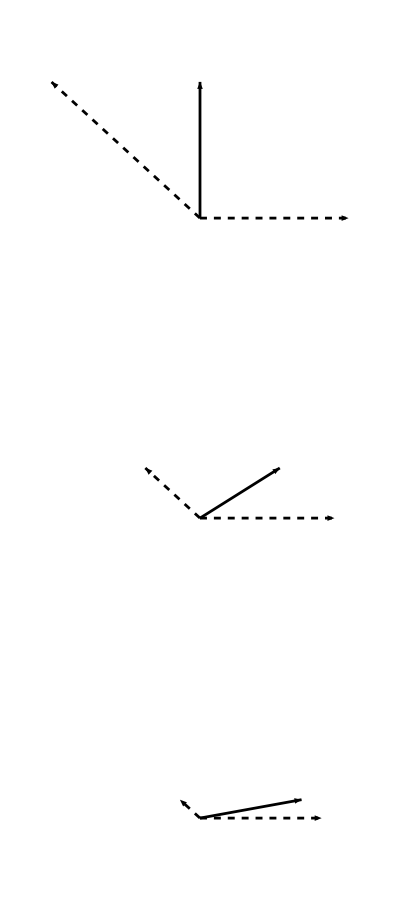

```mathematica
ϵ=0.25;
x1[t_]:=Exp[-t]*{1,0}
x2[t_]:=Exp[-10*t]*{-1,ϵ}
x[t_]:=x1[t]+x2[t]
p0=Grid@Transpose[{Table[Graphics[{AbsoluteThickness[2],Arrowheads[0.07],Arrow[{{0,0},x[t]}],Dashed, Arrow[{{0,0},x1[t]}],Arrow[{{0,0},x2[t]}]},PlotRange->{{-1.1,1.1},{-0.1,ϵ+0.1}},ImageSize->250],{t,0,0.2,0.1}]}]
```

data/h2o2/3/

{18,376,1.3744,12639,10}

4.46967×10^-15

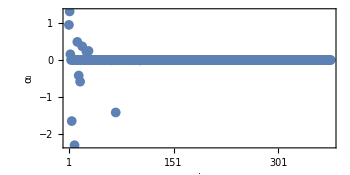
-Graphics- | -Graphics-
-Graphics-

fig2.pdf

```mathematica
filebase="data/h2o2/3/"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=1;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
p=Grid[{{Grid[{{ListPlot[Reverse[α],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript["α",i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],p0}}]},{p}}]
Export["fig2.pdf",p]
```

## Runtimes

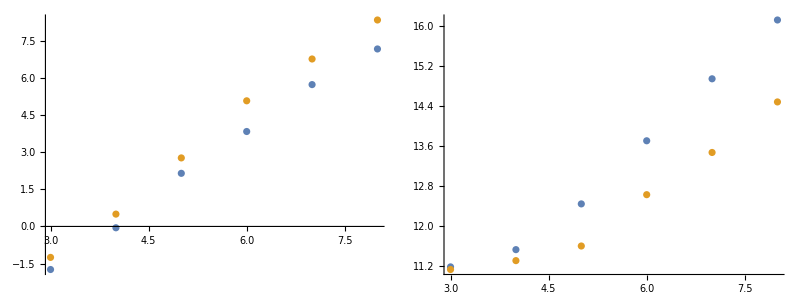

16.8152

79.4483

62111.7

5541.84

```mathematica
Grid[{{ListPlot[{{#[[1]],Log[#[[2]]]}&/@Import["lsoda.dat"],{#[[1]],Log[#[[2]]]}&/@Import["bdf.dat"]}],ListPlot[{{#[[1]],Log[#[[3]]]}&/@Import["lsoda.dat"],{#[[1]],Log[#[[3]]]}&/@Import["bdf.dat"]}]}}]
Exp[Fit[{#[[1]],Log[#[[2]]]}&/@Import["lsoda.dat"],{1,x},x]]/3600/.x->10
Exp[Fit[{#[[1]],Log[#[[2]]]}&/@Import["bdf.dat"],{1,x},x]]/3600/.x->10
Exp[Fit[{#[[1]],Log[#[[3]]]}&/@Import["lsoda.dat"],{1,x},x]]/2^10/.x->10
Exp[Fit[{#[[1]],Log[#[[3]]]}&/@Import["bdf.dat"],{1,x},x]]/2^10/.x->10
```

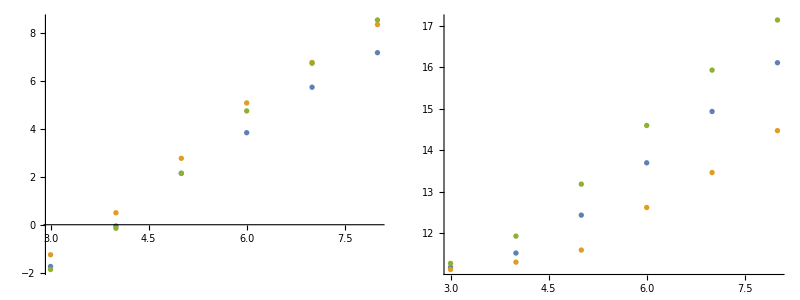

```mathematica
Grid[{{ListPlot[{{#[[1]],Log[#[[2]]]}&/@Import["lsoda.dat"],{#[[1]],Log[#[[2]]]}&/@Import["bdf.dat"],{#[[1]],Log[#[[2]]]}&/@Import["eigenvalues.dat"],{#[[1]],Log[#[[2]]]}&/@Import["eigenvalues2.dat"]},ImageSize->300],ListPlot[{{#[[1]],Log[#[[3]]]}&/@Import["lsoda.dat"],{#[[1]],Log[#[[3]]]}&/@Import["bdf.dat"],{#[[1]],Log[#[[3]]]}&/@Import["eigenvalues.dat"],{#[[1]],Log[#[[3]]]}&/@Import["eigenvalues2.dat"]},ImageSize->300]}}]
```

## Kmatrix

```mathematica
filebase="data/grimech"
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
Nt=Length[times];
evals=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2],Length[times]];
ns=Length[evals];
matrices=Partition[Partition[BinaryReadList[filebase<>"matrices2.npy","Real64"][[17;;-1]],ns],ns];
```

data/grimech

{100,53,53}

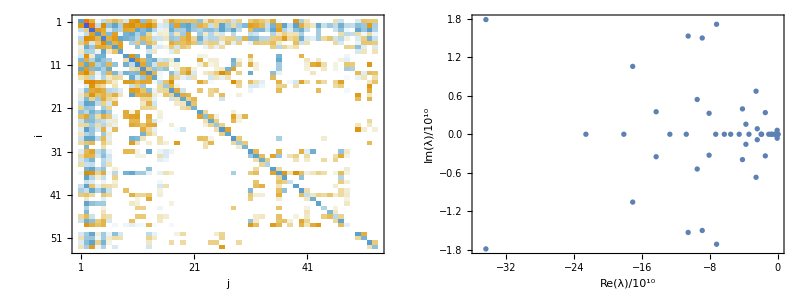

```mathematica
Dimensions[matrices]
p=Grid[{{MatrixPlot[matrices[[1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices[[1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]}}]
```

{53,100}

ListPlot::opttf: Value of option Joined -> true should be True or False.

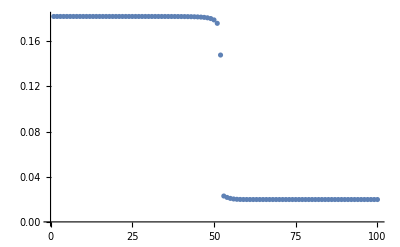

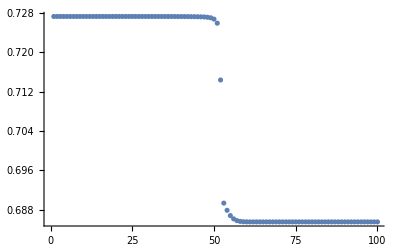

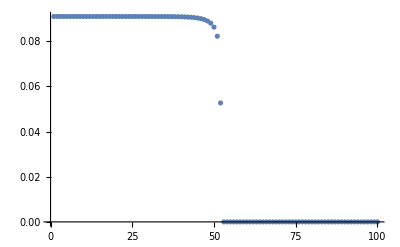

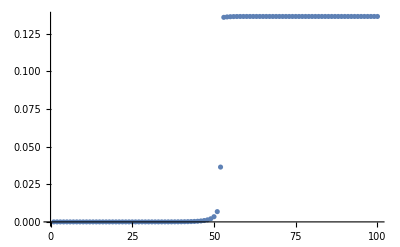

```mathematica
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],ns]];
Dimensions[concentrations]
ListPlot[concentrations[[4]],PlotRange->All,Joined->true]
ListPlot[concentrations[[48]],PlotRange->All]
ListPlot[concentrations[[14]],PlotRange->All]
ListPlot[concentrations[[6]],PlotRange->All]
```